# functions

```mathematica
(* finds numerical value of λ parameter of triangle electrostatic center X(5626) *)
(* based on the Cartesian coordinates of triangle vertices *)
(* default value of Precision option is 12 decimal places *)
FindElectrostaticLambda[{{xa_,ya_},{xb_,yb_},{xc_,yc_}},OptionsPattern[{Precision->12}]]:=
Module[{a,b,c,s,l,u,v,w,left,right,sol,p},
a=Norm[{xc,yc}-{xb,yb}];b=Norm[{xa,ya}-{xc,yc}];c=Norm[{xb,yb}-{xa,ya}];
u=a*Coth[(a*l)/(a+b+c)];v=b*Coth[(b*l)/(a+b+c)];w=c*Coth[(c*l)/(a+b+c)];
left=√((u^2-a^2)(a^2-(v-w)^2))+√((v^2-b^2)(b^2-(w-u)^2))+√((w^2-c^2)(c^2-(u-v)^2));
right=√(2(a^2 b^2+b^2 c^2+c^2 a^2)-(a^4+b^4+c^4));
sol=FindRoot[left==right,{l,1},AccuracyGoal->OptionValue[Precision],PrecisionGoal->OptionValue[Precision],WorkingPrecision->OptionValue[Precision],MaxIterations->10000];
Return[l/.sol];
]

(* computes a point on electrostatic line of the triangle *)
(* based on the λ parameter and Cartesian coordinates of triangle vertices *)
(* returns electrostatic center X(5626) if electrostatic center's λ is used *)
ElectrostaticLine[{{xa_,ya_},{xb_,yb_},{xc_,yc_}},l_]:=
Module[{a,b,c,u,v,w,ka,kb,kc,dx,dy,nx,ny},
a=Norm[{xc,yc}-{xb,yb}];b=Norm[{xa,ya}-{xc,yc}];c=Norm[{xb,yb}-{xa,ya}];
u=a*Coth[(a*l)/(a+b+c)];v=b*Coth[(b*l)/(a+b+c)];w=c*Coth[(c*l)/(a+b+c)];
ka=xa^2+ya^2-v*w;kb=xb^2+yb^2-w*u;kc=xc^2+yc^2-u*v;

dx=ka(yb-yc)+kb(yc-ya)+kc(ya-yb);
nx=2(xa(yb-yc)+xb(yc-ya)+xc(ya-yb));

dy=ka(xb-xc)+kb(xc-xa)+kc(xa-xb);
ny=2(ya(xb-xc)+yb(xc-xa)+yc(xa-xb));

Return[{dx/nx,dy/ny}];
]

(* returns Cartesian coordinates of triangle electrostatic center X(5626) *)
(* triangle is defined with Cartesian coordinates of its vertices *)
(* default value of Precision option is 12 decimal places *)
FindElectrostaticCenter[{{xa_,ya_},{xb_,yb_},{xc_,yc_}},OptionsPattern[{Precision->12}]]:=ElectrostaticLine[{{xa,ya},{xb,yb},{xc,yc}},FindElectrostaticLambda[{{xa,ya},{xb,yb},{xc,yc}},Precision->OptionValue[Precision]]]
```

# examples

```mathematica
FindElectrostaticCenter[{{-1,0},{2,0},{0,2}}]
```

{0.2725579069,0.70414818972}

```mathematica
FindElectrostaticLambda[{{-1,0},{2,0},{0,2}},Precision->50]
```

4.010297202743007522718690055346628610375659507713

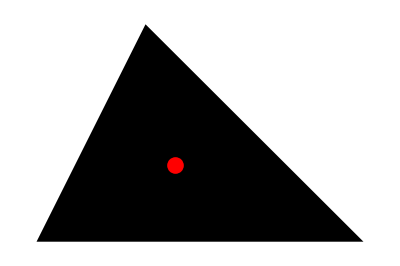

```mathematica
triangle={{-1,0},{2,0},{0,2}};
electroCenter=FindElectrostaticCenter[triangle];
Show[{
Graphics[Polygon[triangle]],
Graphics[{RGBColor[1,0,0],PointSize[.03],Point[electroCenter]}]
}]
```